# Esercizi 1-2 Lingue stabilità e instabilità di equilibri.

## Lingue di stabilità per l’equilibrio superiore del pendolo forzato con supporto oscillante.

Consideriamo un pendolo di lunghezza l forzato in modo tale che il suo punto di sospensione oscilli periodicamente con frequenza Ω. 
La quota del punto di sospensione al tempo t è allora data da una funzione periodica di periodo 2π/Ω, supponiamo sia f(t) = a cos(Ωt).

Come si è visto nel corso, scelta come coordinata lagrangiana l’angolo θ tra la verticale discendente ed il pendolo, la Lagrangiana del sistema è, a meno di una costante motiplicativa e di termini additivi funzione della sola t, che quindi danno un contributo nullo alle equazioni di Lagrange:

L(θ,θ’,t) = 1/2 l (θ’)^2 + f’(t) θ’ sinθ + g cosθ.

Di conseguenza, l’equazione del moto è

θ’’ + (α^2 - k cos t) sinθ = 0,

con α = ω/Ω   e k = a/l.

Il sistema del primo ordine equivalente all’equazione del moto ammette i due equilibri (0,0) e (π,0) nello spazio delle fasi S^1 x R. Vogliamo studiare le proprietà di stabilità dell’equilibrio superiore, (π,0), al variare dei parametri α e k.

Poiché il campo vettoriale è periodico di periodo T = 2π, possiamo considerare l’equilibrio come punto fisso della mappa di avanzamento di un periodo e studiarne la stabilità attraverso lo spettro della linearizzazione: abbiamo visto infatti che è sufficiente studiare il modulo della traccia (che è funzione dei parametri α e k).

La linearizzazione della mappa di avanzamento di un periodo è la soluzione al tempo T dell’equazione differenziale matriciale K’ = X’(π,0) K, ove la K dipende dal tempo e ha come dato iniziale la matrice identità. Osserviamo che:

X’(π,0) = (0 | 1
α^2 -k cos (t) | 0).

Definiamo dapprima il campo vettoriale che consente di risolvere l’equazione per la linearizzazione della mappa di avanzamento di un periodo.

```mathematica
X[{α_,k_}][{x_,v_,t_}]:={v,(α^2-k Cos[t])x,1}
```

```mathematica
Algo2[h_,par_][z_]:=z+h X[par][z+h/2 X[par][z]]
```

```mathematica
Algo2[h,{α,k}][{x,v,t}]/.{x->xvt[[1]] , v->xvt[[2]],  t-> xvt[[3]] }
```

```mathematica
Algoc=Compile[   { h, α , k, {xvt,_Real,1}  } ,
           {xvt⟦1⟧+h (1/2 h (α^2-k Cos[xvt⟦3⟧]) xvt⟦1⟧+xvt⟦2⟧),xvt⟦2⟧+h (α^2-k Cos[h/2+xvt⟦3⟧]) (xvt⟦1⟧+1/2 h xvt⟦2⟧),h+xvt⟦3⟧} ]
```

Lavoreremo con la versione compilata dell’algoritmo Runge-Kutta di ordine 2. Compiliamo anche la mappa di avanzamento di un periodo (ricavata iterando T/h volte l’algoritmo di RK-2)

```mathematica
MAPc = Compile[{{N,_Integer} ,α,k,{xv,_Real,1}}, 
                            Delete[    Nest[ Algoc[(2Pi)/N,α,k,#]&,Append[xv,0],N] ,-1] ];
```

Definiamo le rimanenti funzioni necessarie al calcolo della traccia della matrice della linearizzazione della mappa di avanzamento di un periodo.

```mathematica
trK[N_,{α_,k_}]:=Abs[  MAPc[N,α,k,{1,0}][[1]] + MAPc[N,α,k,{0,1}][[2]]  ];
aktr[N_][par_]:={par,trK[N,par]}; (*per ogni coppia di parametri calcola la traccia*)
sel[lst_]:=Map[First,  Select[  lst  , #[[2]]<=2 &]  ](*Seleziona i parametri {α,k} per cui si ha traccia ≤2*)
```

Scegliamo un alto numero di coppie di parametri {α,k} nella zona in cui vogliamo indagare la presenza di lingue di stabilità per il punto di instabilità.

```mathematica
tab=Table[   {RandomReal[{0,1}] , RandomReal[{0,2}] } ,50000];
```

```mathematica
stab=sel[ParallelMap[aktr[400],tab]];
```

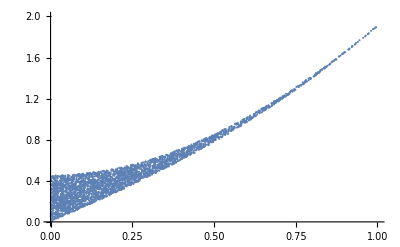

```mathematica
ListPlot[ stab, PlotRange->{ {0,1},{0,2}} ]
```

Si nota dal grafico ottenuto una lingua di instabilità, come  nell’ipotesi che avevamo avanzato nello studio teorico delle lingue di stabilità/instabilità. Come previsto la lungua si ha vicino all’origine, poichè in effetti sull’asse k=0 si dimostra che ogni punto del piano dei parametri ha un intorno in cui i parametri sono ancora associati a instabilità.

Proviamo a vedere se si vedono ulteriori lingue di instabilità per valori più alti di k.

```mathematica
tab2=Table[{RandomReal[{0,1}] , RandomReal[{0,4}] } ,80000];
```

```mathematica
stab=sel[ParallelMap[aktr[300],tab2]];
```

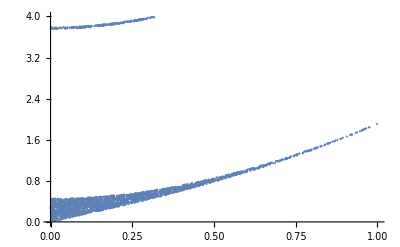

```mathematica
ListPlot[ stab, PlotRange->{ {0,1},{0,4}} ]
```

Compare una seconda lungua di stabilità attorno a k=3.8 e si osserva che pare avere una “dimensione” notevolmente minore della “lungua” che si ha per valori di k più bassi.

## Lungue di intsabilità per l’equilibrio inferiore del pendolo di lunghezza variabile.

Consideriamo nel piano xz un pendolo di lunghezza variabile 
h(t) = h_0+ a cos(Ωt), con a, Ω > 0 e h_0 > a.

Determiniamo innanzitutto la Lagrangiana del sistema, per scrivere l’equazione del moto. 
Scegliendo come coordinata lagrangiana l’angolo θ tra la verticale discendente ed il pendolo, le coordinate del punto materiale sono
x = h(t) sinθ,  y = 0,  z = -h(t) cosθ,
da cui
x’ = h’(t) sinθ + h(t) θ’ cosθ
y’ = 0
z’ = -h’(t) cosθ + h(t) θ’ sinθ.
L’energia potenziale dovuta alla forza peso è V(θ,t) = -mg h(t) cosθ, l’energia cinetica invece risulta T(θ,θ’,t) = 1/2m (h’(t)^2 + (h(t) θ’)^2).

Dunque la Lagrangiana del sistema è, a meno di una costante moltiplicativa e di termini additivi funzione della sola t, che daranno un contributo nullo alle equazioni di Lagrange,

L(θ,θ’,t) = 1/2(h(t) θ’)^2 + g h(t) cosθ.

L’equazione del moto è pertanto 

θ’’ + 2(h'(t))/(h(t))θ’ + g/(h(t)) sinθ = 0.

Il sistema del primo ordine equivalente a questa equazione è dato dalle equazioni θ’ = v, v’ = -2(h'(t))/(h(t))θ’ - g/(h(t))sinθ, ed ammette i due equilibri (π,0) e (0,0).

Vogliamo studiare la stabilità dell’equilibrio inferiore (0,0) al variare dei parametri Ω e a.

Il campo vettoriale è periodico di periodo T = 2π/Ω. Di conseguenza, è possibile pensare l’equilibrio come punto fisso della mappa di avanzamento di un periodo e determinarne la stabilità studiando lo spettro della linearizzazione (è sufficiente studiare il modulo della traccia).

La linearizzazione della mappa di avanzamento di un periodo è la soluzione al tempo T dell’equazione differenziale matriciale K’ = X’(0,0) K, con la condizione iniziale che K(0) sia la matrice identità.
Osserviamo che  X’(θ,v) = (0 | 1
-g/(h(t))cos θ | -2(h'(t))/(h(t))), dunque la linearizzazione all’equilibrio (0,0) è data da X’(0,0) = (0 | 1
-g/(h(t)) | -2(h'(t))/(h(t))), con h’(t) = -a Ω sin(Ωt).

Il procedimento è simile a quanto visto sopra nel caso precedente.

```mathematica
g=9.81;
l=g/4;
```

```mathematica
XL[{a_,om_}][{x_,v_,t_}]:={v,(-g x+2a om v Sin[om t])/(l+a Cos[om t]),1};
AlgoL[h_,par_][z_]:=z+h XL[par][z+h/2 XL[par][z]]; (*la variabile par_ contiene i due parametri a e Ω*)
```

```mathematica
AlgoL[H,{a,om}][{x,v,t}]/.{x->xvt[[1]] , v->xvt[[2]],  t-> xvt[[3]] }
```

```mathematica
AlgoLC=Compile[ {H, {a,_Real}, {om,_Real}, {xvt,_Real,1}  } ,{xvt⟦1⟧+H (xvt⟦2⟧+(H (-9.81 xvt⟦1⟧+2 a om xvt⟦2⟧ Sin[om xvt⟦3⟧]))/(2 (2.4525+a Cos[om xvt⟦3⟧]))),xvt⟦2⟧+(H (-9.81 (xvt⟦1⟧+1/2 H xvt⟦2⟧)+2 a om (xvt⟦2⟧+(H (-9.81 xvt⟦1⟧+2 a om xvt⟦2⟧ Sin[om xvt⟦3⟧]))/(2 (2.4525+a Cos[om xvt⟦3⟧]))) Sin[om (H/2+xvt⟦3⟧)]))/(2.4525+a Cos[om (H/2+xvt⟦3⟧)]),H+xvt⟦3⟧}];
```

```mathematica
MAPcL = Compile[{{N,_Integer} ,a,om,{xv,_Real,1}}, 
                            Delete[    Nest[ AlgoLC[(2.Pi)/(N om),a,om,#]&,Append[xv,0],N] ,-1] ];
```

```mathematica
trKL[N_,{a_,om_}]:=Abs[  MAPcL[N,a,om,{1,0}][[1]] + MAPcL[N,a,om,{0,1}][[2]]  ];
aktrL[N_][par_]:={par,trKL[N,par]}; (*per ogni coppia di parametri calcola la traccia*)
selL[lst_]:=Map[First,  Select[  lst  , #[[2]]>2 &]  ](*Seleziona i parametri {α,k} per cui si ha traccia ≤2*)
```

Ora, se la frontiera della regione di instabilità tocca l’asse a=0, questo deve avvenire nei punti (Ω,0) nei quali la traccia della linearizzazione della mappa di avanzamento di un periodo sia pari a 2. 
Non è difficile determinare tali punti: per a=0, la linearizzazione del campo vettoriale è l’equazione dell’oscillatore armonico u’’ + α^2 u =0, con α = √(g/h_0). Calcolando esplicitamente il modulo della traccia della linearizzazione, si trova che i punti (Ω_n,0) in cui tale modulo vale 2 sono quelli tali che Ω_n = 2α/n, con n intero.
Abbiamo scelto h_0 = g/4, cosicché α = 2 e Ω_n= 4/n, n intero. Dunque, per n=1, la regione di instabilità tocca l’asse a=0 in (4,0); se n=2, in (2,0); se n=4, in (1,0).

Vogliamo ora descrivere numericamente le regioni di instabilità.

Eseguiamo l’analisi delle lingue di instabilità come nel caso precedente per la stabilità: scegliamo i valori random dei parametri nella zona da studiare e verifichiamo per quali di essi si ha la traccia della linearizzazione della mappa di avanzamento di un periodo >2 (instabilità). Scegliamo i punti nel piano dei parametri in cui valutare la traccia della linearizzazione.

```mathematica
p1=Table[   {RandomReal[{0,.3}] , RandomReal[{3.5,4.5}] } ,10000];
p2=Table[   {RandomReal[{0,.3}] , RandomReal[{1.8,2.1}] } ,20000];
p3=Table[   {RandomReal[{0,.3}] , RandomReal[{0.9,1.1}] } ,50000];
inst=selL[ParallelMap[aktrL[300],Union[p1,p2,p3]]];
```

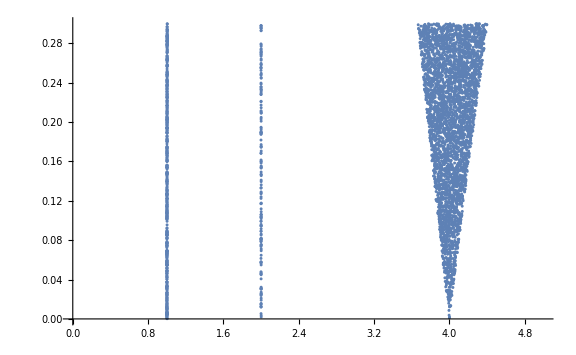

```mathematica
ListPlot[ Map[Reverse,inst], PlotRange->{ {0,5},{0,.3}} ,ImageSize->Large] (*Il comando reverse traspone le coppie di parametri: avrò sulle ascisse *)
```

Si notano le lingue di instabilità che arrivano a toccare l’asse a=0: ho ristretto la scelta dei punti alle zone dove mi aspetto lingue di instabilità (per valori  Ω=4,2,1), ma le lingue più strette sembrano dei rettangoli (probabilmente si tratta di qualche problema di precisione).